#### Problems for 12/08/17 Oleksandr Yardas

#### GT3.4

We are now assuming that in the game Rock-Paper-Scissors (RPS), the Payoff Matrix looks like

```mathematica
A1={{a,-1,1},{1,a,-1},{-1,1,a}};w1={{x},{y},{1-x-y}};w1T=Transpose[w1];
```

```mathematica
MatrixForm[A1]
```

(a | -1 | 1
1 | a | -1
-1 | 1 | a)

Our strategy profile is still

```mathematica
MatrixForm[w1]
```

(x
y
1-x-y)

```mathematica
MatrixForm[Expand[A1.w1]]
```

(1-x+a x-2 y
-1+2 x+y+a y
a-x-a x+y-a y)

The expected payoffs for these strategies are p11, p12, and p13, such that

```mathematica
Clear[p11,p12,p13]
```

```mathematica
p11[x_,y_]:=1-x+a x-2 y;
p12[x_,y_]=-1+2 x+y+a y;
p13[x_,y_]:=a-x-a x+y-a y
```

The expected payoff to a random player in the population is p such that

```mathematica
p1[x_,y_]:={{a-2 a x+2 a x^2-2 a y+2 a x y+2 a y^2}}
```

This means that the replicator equations are  P and Q such that

```mathematica
P1[x_,y_]:=x*(p11[x,y]-p1[x,y]);
Q1[x_,y_]:=y*(p12[x,y]-p1[x,y])
```

```mathematica
Expand[P1[x,y]]
```

{{x-a x-x^2+3 a x^2-2 a x^3-2 x y+2 a x y-2 a x^2 y-2 a x y^2}}

```mathematica
Expand[Q1[x,y]]
```

{{-y-a y+2 x y+2 a x y-2 a x^2 y+y^2+3 a y^2-2 a x y^2-2 a y^3}}

The equilibra cna be found by using Solve. If a>0, we get

```mathematica
Solve[{P1[x,y]==0,Q1[x,y]==0,x>0,y>0,1-x-y>0,a>0},{x,y}]
```

{{x→ConditionalExpression[1/3,a>0],y→ConditionalExpression[1/3,a>0]}}

whereas if a<0, we get

```mathematica
Solve[{P1[x,y]==0,Q1[x,y]==0,x>0,y>0,1-x-y>0,a<0},{x,y}]
```

{{x→ConditionalExpression[1/3,-1<a<0],y→ConditionalExpression[1/3,-1<a<0]},{x→ConditionalExpression[1/3,a<-1],y→ConditionalExpression[1/3,a<-1]}}

Notice that both of these are the mixed nash equilibria for RPS, that is w={{1/3},{1/3},{1/3}}. To assess the stabuility of this equilibirum in the case where a>0 and where a<0, we need to find the jacobian of the system (P1,Q1):

```mathematica
Jac:={{D[P1[x,y], x],D[P1[x,y], y]},{D[Q1[x,y], x],D[Q1[x,y], y]}}
```

```mathematica
Jac/.{x->1/3,y->1/3}
```

```mathematica
MatrixForm[Expand[{{1/3 (-1+a),-2/3},{2/3,(1+a)/3}}]]
```

(-1/3+a/3 | -2/3
2/3 | 1/3+a/3)

This Jacobian has eigenvalues:

```mathematica
Expand[Eigenvalues[({{-1/3+a/3, -2/3}, {2/3, 1/3+a/3}})]]
```

{-ⅈ/(√3)+a/3,ⅈ/(√3)+a/3}

Notice we have eigenvalues of the form L+/- i*u. If a>0, L>0, which means (1/3,1/3) is an unstable sprial point. However, if a<0, L<0, which means that (1/3,1/3) is an asymptotically stable sprial point. Plotting to confirm our results:

```mathematica
p11a[x_,y_]:=1-2 y;
p12a[x_,y_]=-1+2* x+2* y;p1a[x_,y_]:={{1-2 * x+2 * x^2-2* y+2* x *y+2* y^2}};p11b[x_,y_]:=1-2*x-2 *y;
p12b[x_,y_]=-1+2 *x;p1b[x_,y_]:={{-1+2 *x-2 * x^2+2 * y-2*x *y-2 *y^2}};
```

```mathematica
P1a[x_,y_]:=x (2 x-2 x^2-2 x y-2 y^2);
Q1a[x_,y_]:=y (-2+4 x-2 x^2+4 y-2 x y-2 y^2);P1b[x_,y_]:=x (2-4 x+2 x^2-4 y+2 x y+2 y^2);
Q1b[x_,y_]:=y (2 x^2-2 y+2 x y+2 y^2)
```

```mathematica
s1a=NDSolve[{x1a'[t]==P1a[x1a[t],y1a[t]],y1a'[t]==Q1a[x1a[t],y1a[t]],x1a[0]==.25,y1a[0]==.25},{x1a,y1a},{t,0,100}];
```

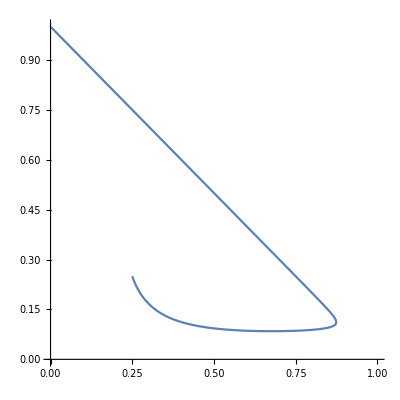

```mathematica
ParametricPlot[Evaluate[{x1a[t],y1a[t]}/.s1a],{t,0,100},PlotRange->{{0,1},{0,1}}]
```

```mathematica
sb=NDSolve[{xb'[t]==Pb[xb[t],yb[t]],yb'[t]==Qb[xb[t],yb[t]],xb[0]==.25,yb[0]==.25},{xb,yb},{t,0,100}];
```

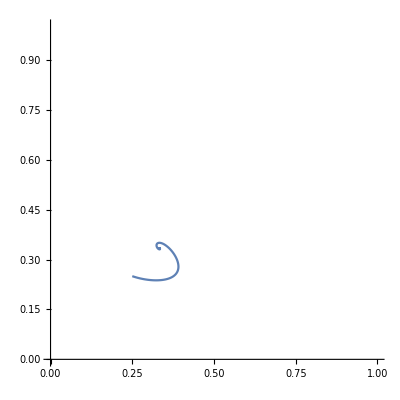

```mathematica
ParametricPlot[Evaluate[{xb[t],yb[t]}/.sb],{t,0,100},PlotRange->{{0,1},{0,1}}]
```

#### Problem GT3.5

We are now assuming that in the game in Exercise 4 of section 2 (E42), the Payoff Matrix looks like

```mathematica
A2={{0,7,3},{-3,7,7},{10,4,-2}};w2={{x},{y},{1-x-y}};w2T=Transpose[w1];
```

```mathematica
w2T.A2.w2
```

```mathematica
Expand[{{x (10 (1-x-y)-3 y)+(1-x-y) (3 x-2 (1-x-y)+7 y)+y (7 x+4 (1-x-y)+7 y)}}]
```

{{-2+17 x-15 x^2+15 y-24 x y-6 y^2}}

```mathematica
MatrixForm[A2]
```

(0 | 7 | 3
-3 | 7 | 7
10 | 4 | -2)

Our strategy profile is still

```mathematica
MatrixForm[w2]
```

(x
y
1-x-y)

```mathematica
MatrixForm[Expand[A2.w2]]
```

(3-3 x+4 y
7-10 x
-2+12 x+6 y)

The expected payoffs for these strategies are p21, p22, and p23, such that

```mathematica
p21[x_,y_]:=3-3 x+4 y;
p22[x_,y_]=7-10 x;
p23[x_,y_]:=-2+12 x+6 y
```

The expected payoff to a random player in the population is p such that

```mathematica
p2[x_,y_]:=-2+17 x-15 x^2+15 y-24 x y-6 y^2
```

This means that the replicator equations are  P and Q such that

```mathematica
P2[x_,y_]:=x*(p21[x,y]-p2[x,y]);
Q2[x_,y_]:=y*(p22[x,y]-p2[x,y])
```

```mathematica
Expand[P2[x,y]]
```

5 x-20 x^2+15 x^3-11 x y+24 x^2 y+6 x y^2

```mathematica
Expand[Q2[x,y]]
```

9 y-27 x y+15 x^2 y-15 y^2+24 x y^2+6 y^3

The equilibra can be found by using Solve.

```mathematica
Solve[{P2[x,y]==0,Q2[x,y]==0,x>0,y>0,1-x-y>0},{x,y}]
```

{{x→6/23,y→25/46}}

Notice that this correspond to the mixed nash equilibria for E42, that is w={{6/23},{25/46},{9/46}}. To assess the stabuility of this equilibirum, we need to find the jacobian of the system (P,Q):

```mathematica
Jac:=D[{P2[x,y],Q2[x,y]},{{x,y}}]
```

```mathematica
Jac/.{x->6/23,y->25/46}
```

{{120/529,246/529},{-3525/1058,-1275/1058}}

```mathematica
MatrixForm[Expand[{{120/529,246/529},{-3525/1058,-1275/1058}}]]
```

(120/529 | 246/529
-3525/1058 | -1275/1058)

This Jacobian has eigenvalues:

```mathematica
Expand[Eigenvalues[({{120/529, 246/529}, {-3525/1058, -1275/1058}})]]
```

{-45/92+(15 ⅈ √39)/92,-45/92-(15 ⅈ √39)/92}

Notice we have eigenvalues of the form L+/- i*u. In this case, L<0, which means that (6/23,25/46) is an asymptotically stable sprial point. Plotting to confirm our results:

```mathematica
s2=NDSolve[{x2'[t]==P2[x2[t],y2[t]],y2'[t]==Q2[x2[t],y2[t]],x2[0]==.25,y2[0]==.25},{x2,y2},{t,0,100}];
```

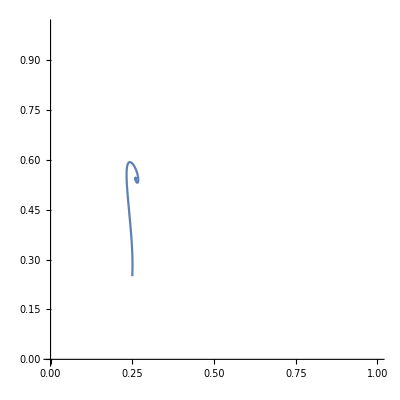

```mathematica
ParametricPlot[Evaluate[{x2[t],y2[t]}/.s2],{t,0,100},PlotRange->{{0,1},{0,1}}]
```